```mathematica
Solve[λ*x^2+a*x+c==0,x]
```

{{x→(-a-√(a^2-4 c λ))/(2 λ)},{x→(-a+√(a^2-4 c λ))/(2 λ)}}

```mathematica
(*Considering V(x)=λx^2+ax+c as pertubation*)
Integrate[(2/L)*(Sin[(n*Pi*x)/L])*(λ^2*x^2+a*x+c),{x,0,L}]
```

(2 (c n^2 π^2-2 L^2 λ^2-((c+a L) n^2 π^2+L^2 (-2+n^2 π^2) λ^2) Cos[n π]+L n π (a+2 L λ^2) Sin[n π]))/(n^3 π^3)

```mathematica
Simplify[1/(n^3 π^3)2 (c n^2 π^2-2 L^2 λ^2-((c+a L) n^2 π^2+L^2 (-2+n^2 π^2) λ^2) Cos[n π]+L n π (a+2 L λ^2) Sin[n π]),Assumptions->n∈Integers]
```

-(2 ((-1+(-1)^n) c n^2 π^2+L ((-1)^n a n^2 π^2+L (2-2 (-1)^n+(-1)^n n^2 π^2) λ^2)))/(n^3 π^3)

```mathematica
(*I assumed that n is an odd integer, the same work has to be done for the even integers, but it is not presented here. The obtained results are presented in the paper*)
```

```mathematica
(*The calculation of the term Energyax2 is based on the results obtained from the linear potential so we calculated in the previous notebook*)
A=(2*0.511*10^6)/(6.58211*10^(-16))^2//N
```

2.35896×10^36

```mathematica
Energyax2=c-(a^(2/3)*2.33811)/(A)^(1/3)+(3*L^2*λ)/5//N
```

-1.75641×10^-12 a^(2/3)+c+0.6 L^2 λ

```mathematica
Energyall=(4 c n^2 π^2+2 L (a n^2 π^2+L (-4+n^2 π^2) λ^2))/(n^3 π^3)//N//Expand
```

(1.27324 c)/n+(0.63662 a L)/n-(0.258012 L^2 λ^2)/n^3+(0.63662 L^2 λ^2)/n

```mathematica
error=Energyall-Energyax2
```

1.75641×10^-12 a^(2/3)-c+(4.18388×10^-36 n^2)/L^2-0.6 L^2 λ-(0.63662 L (a+L λ^2))/n

```mathematica
1.75641*10^(-12) a^(2/3)-c+(4.18388*10^(-36) n^2)/L^2-0.6* L^2 λ-(0.63662* L (a+L λ^2))/n;


error1=-c+(4.18388*10^(-36)* n^2)/L^2-(0.63662*L (a))/n-0.6* L^2 λ//Simplify
```

-c-(0.63662 a L)/n+(4.18388×10^-36 n^2)/L^2-0.6 L^2 λ

```mathematica
error2=-c+(4.18388*10^(-36)* n^2)/L^2-(0.63662*L (a))/n
```

```mathematica
(*Calculations for the Frobenius method*)
```

```mathematica
ξ=20;
f=∑_(k=-ξ)^-1 B*Indexed[c,k+ξ]*x^(k+ξ)+∑_(k=-(ξ+2))^-1 (k+ξ+1)*(k+ξ+2)*Indexed[c,k+ξ+2]*x^(k+ξ)//Expand
```

Indexed::ind: The index 0 is not a nonzero integer.

B Indexed[c,0]+B x c1+2 c2+B x^2 c2+6 x c3+B x^3 c3+12 x^2 c4+B x^4 c4+20 x^3 c5+B x^5 c5+30 x^4 c6+B x^6 c6+42 x^5 c7+B x^7 c7+56 x^6 c8+B x^8 c8+72 x^7 c9+B x^9 c9+90 x^8 c10+B x^10 c10+110 x^9 c11+B x^11 c11+132 x^10 c12+B x^12 c12+156 x^11 c13+B x^13 c13+182 x^12 c14+B x^14 c14+210 x^13 c15+B x^15 c15+240 x^14 c16+B x^16 c16+272 x^15 c17+B x^17 c17+306 x^16 c18+B x^18 c18+342 x^17 c19+B x^19 c19+380 x^18 c20+420 x^19 c21

```mathematica
CoefficientList[f,x]
```

{B Indexed[c,0]+2 c2,B c1+6 c3,B c2+12 c4,B c3+20 c5,B c4+30 c6,B c5+42 c7,B c6+56 c8,B c7+72 c9,B c8+90 c10,B c9+110 c11,B c10+132 c12,B c11+156 c13,B c12+182 c14,B c13+210 c15,B c14+240 c16,B c15+272 c17,B c16+306 c18,B c17+342 c19,B c18+380 c20,B c19+420 c21}

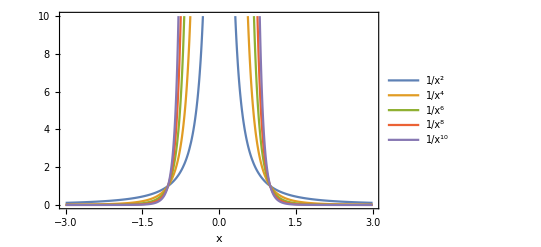

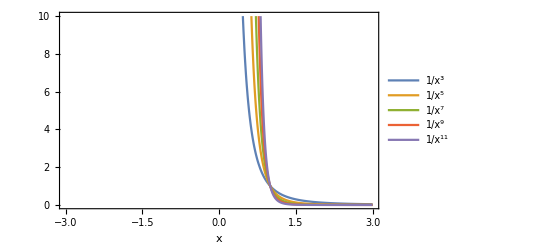

```mathematica
Plot[{x^-2,x^-4,x^-6,x^-8,x^-10},{x,-3,3},PlotLegends->"Expressions",Frame->True,PlotRange->{0,10},FrameLabel->{"x"}]
Plot[{x^-3,x^-5,x^-7,x^-9,x^-11},{x,-3,3},PlotLegends->"Expressions",Frame->True,PlotRange->{0,10},FrameLabel->{"x"}]
```

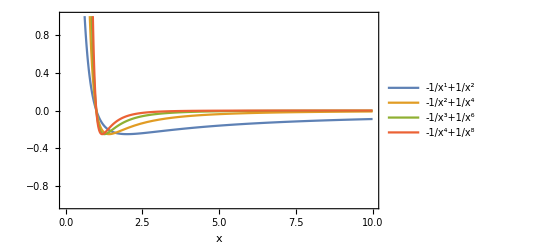

```mathematica
Plot[{-1/x^1+1/x^2,-1/x^2+1/x^4,-1/x^3+1/x^6,-1/x^4+1/x^8},{x,0,10},PlotLegends->"Expressions",Frame->True,PlotRange->{-1,1},FrameLabel->{"x"}]
```

```mathematica
v[x_]:=-a/x^ξ+b/x^(2*ξ)
```

```mathematica
v'[x]
```

-2 b x^(-1-2 ξ) ξ+a x^(-1-ξ) ξ

```mathematica
Solve[v'[x]==0,x]
Solve[v[x]==0,x]
```

{{x→2^(1/ξ) a^(-1/ξ) b^(1/ξ)}}

{{x→a^(-1/ξ) b^(1/ξ)}}

```mathematica
v[2^(1/ξ) a^(-1/ξ) b^(1/ξ) ]
```

```mathematica
v0=b (2^(1/ξ) a^(-1/ξ) b^(1/ξ))^(-2 ξ)-a (2^(1/ξ) a^(-1/ξ) b^(1/ξ))^-ξ//Simplify
```

(2^(1/ξ) a^(-1/ξ) b^(1/ξ))^(-2 ξ) (b-a (2^(1/ξ) a^(-1/ξ) b^(1/ξ))^ξ)

```mathematica
x0=a^(-1/ξ) b^(1/ξ)
```

a^(-1/ξ) b^(1/ξ)

```mathematica
Integrate[v[x],{x,x0,L}]
```

ConditionalExpression[L^(1-2 ξ) (1/(1-2 ξ)+L^ξ/(-1+ξ)), Re[ξ]<1/2]

```mathematica
Solve[v0==13.6,a]
```